# Quadratic Penalty Methods and Augmented Lagrangians

### Sensitivity: 1D

We are going to look at a 1D inequality constrained optimization problem
		min_(-2≤x≤3) f(x)
and we want to understand what the multipliers mean.

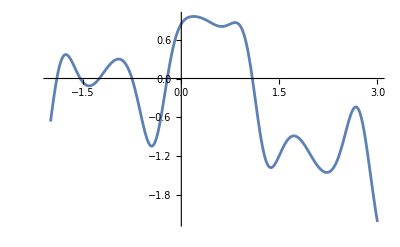

```mathematica
f[x_]:=  Sin[3x+Cos[4x]]-0.2 x^2;
Plot[f[x],{x,-2,3}]
```

We have two inequality constraints.  In our format we have
	x | + | 2 | ≥ | 0
3 | - | x | ≥ | 0
Both end points are KKT points.

For small δ_1 and δ_2 the modified constraint  x+2≥δ_1 and 3-x≥δ_2 gives modified KKT points 
	x_1(δ_1) | = | -2 | + | δ_1
x_2(δ_2) | = | 3 | - | δ_2 
at the modified end points.  Note our sign convention means increasing δ_1 or δ_2 shrinks the feasible set.

The function values at the boundary KKT points are f(-2+δ_1) and f(3-δ_2) so
	d/dδ_1 f(x_1)=f'(x_1)(1)  and d/dδ_2 f(x_2)=f'(x_2)(-1)

Note, we could also have described our constraints as 
	3x | + | 6 | ≥ | 0
12 | - | 4x | ≥ | 0
We want to be able to understand the dependence of 
	h(δ)=min_(x∈Ω(δ)) f(x)
where
	Ω(δ):={x∈ℝ^n:  c_i(x) | = | δ_i | for | i∈ℰ
c_i(x) | ≥ | δ_i | for | i∈ℐ} 
What we are going to be able to work out is that at a KKT point the Lagrange Multipliers satisfy
	dh/dδ_i|_(δ=0)=λ_i
Remember at inactive constraints λ_i=0. In other words the multipliers describe how sensitive the minimum is to the constraints at KKT points. since the global minimizer is a KKT point the multipliers at the global min are the sensitivities of 
	min_(x∈Ω(0)) f(x)

### Multiplier Interpretation: 2D

With a 2D quadratic model with linear constraints we can see exactly what multipliers do.

```mathematica
Clear[c]
n=2;
A=RandomReal[{-1,1},{2,2}];A=A+Aᵀ; g=0.1RandomReal[{-1,1},n];
B[1]={-1,1};B[2]={2,-1};B[3]={3,1};B[4]={-3,-2};
c[{b1_,b2_,b3_,b4_}][{x1_,x2_}]:= And[B[1].{x1,x2}>b1,B[2].{x1,x2}>b2, B[3].{x1,x2}>b3,B[4].{x1,x2}>b4]
f[x_]:=0.5 x.A.x+g.x
Manipulate[
ContourPlot[f[{x1,x2}],{x1,-0.6,0.8},{x2,-1.1,1.1},
Contours->30,
ContourLabels->True,
RegionFunction->Function[{x1,x2},c[{b1,b2,b3,b4}][{x1,x2}]]],
{{b1,-1},-1.2,-0.8},
{{b2,-1},-1.2,-0.8},
{{b3,-1},-1.2,-0.8},
{{b4,-2},-2.1,-1.9}]
```

Complementary slackness means

λ_i c_i[x]=0 for all i

An active and “Strictly Complementary” (SC) constraint has non-zero multiplier λ_i≠0

If c_i[x]≥0 is SC then changing to c_i[x]≥δ_i alters minima.

If c_i[x]=0 is SC then changing to c_i[x]=δ_i alters minima.

The multipliers give the sensitivities.

Our linear constraint set is defined by a vector δ~0∈ℝ^4
	Ω(δ)={x∈ℝ^2: B[i].x+b_i-δ_i≥0  for i∈ℐ={1,2,3,4}}
We have four inequality constraints and no equality constraints

In 2D I have a maximum of 2 genuinely active constraints.

2 active SC constraints. “Corner”

1 active SC constraint. “Edge”

0 active SCconstraints “Interior”

At a KKT point x_* for δ=0 we have ∇f(x_*)=∑_(i∈𝒜_0(x_*)) λ_i∇c_i(x^*) where c_i(x)=B_i.x+b_i-δ_i

For δ small and SC constraints the KKT point varies smoothly with δ and 𝒜_0(x^*)=𝒜_δ(x_*(δ))

For SC constraints all we really need to do is work out how the KKT point varies with δ for a fixed active set 𝒜_0(x^*)

In 2D

2 active SC constraints say {i,j}={1,3} determine x_*(d) from the linear equations
	B_i.x | + | b_i | = | δ_i
B_j.x | + | b_j | = | δ_j   or equivalently B_i.x | = | δ_i-b_i
B_j.x | = | δ_j-b_j 
Constraint qualifications e.g. LICQ ensures a unique solution. The chain rule and KKT equation gives the claimed sensitivities for small δ.

1 SC say i=1 gives the single linear equation
	B_i.x | + | b_i | = | δ_i
The second equation is ∇f(x_*)=A.x+g must be perpendicular to B_i.  The unique solution of 
	B_i.x | + | b_i | = | δ_i
A.x.B_i | + | g.B_i | = | 0	or equivalentlyB_i.x | = | δ_i-b_i
A.x.B_i | = | -g.B_i 
The chain rule and KKT equation gives the claimed sensitivities for small δ.

0 SC.  Interior KKT points do not depend on the constraints for small δ.

### Quadratic Penalization: 1D

We are going to build a 1D Quadratic Penalty Newton method.

Quadratic Penalization refers to adding a piecewise quadratic penalty term to an objective function f to enforce 
(or maybe just encourage) satisfaction of a constraint.  For inequality constraints this technique allows non-feasible 
points and requires large values of the penalization parameter. We are going to do a 1D problem
	min_(-2≤x≤3) f(x)
with an updating local quadratic approximation
	f(x)≈ f_k+df_k(x-x_k)+0.5(ddf_k(x-x_k))^2
Our standard quadratic penalty term is μ_k p(x) where
	p(x)=c(-2,"+",x)+c(3,"-",x)
where 
	c(a,"+",x)=0.5{(x-a)^2 | if | x<a
0 | if | x≥a	 
and 
	c(a,"-",x)=0.5{(x-a)^2 | if | x>a
0 | if | x≤a

```mathematica
c[a_,"+",x_]:=0.5 Which[x<a,(x-a)^2,True,0]
c[a_,"-",x_]:=0.5 Which[x>a,(x-a)^2,True,0]
f[x_]:=  Sin[3x+Cos[4x]]-0.2 x^2;
p[x_]:=c[-2,"+",x]+c[3,"-",x]
Manipulate[
Plot[{f[x],f[x]+μ p[x]},{x, -3,4},PlotRange->{-3.2,1.2},GridLines->Automatic],
{{μ,1},0,100}]
```

At each step we have an x_k and a μ_k.  We get the next point 
	x_(k+1)=argmin g_k+dg_k(x-x_k)+0.5(ddg_k(x-x_k))^2
where 
	g_k | = | f(x_k) | + | μ_k p(x_k)
dg_k | = | df(x_k) | + | μ_k dp(x_k)
ddg_k | = | ddf(x_k) | + | μ_k ddp(x_k)
Then choose μ_(k+1)>μ_k and repeat the process.

```mathematica
g[μ_][x_]:= f[x]+μ p[x]
q[μ_,xk_][x_]:=g[μ][xk]+g[μ]'[xk](x-xk)+0.5g[μ]''[xk](x-xk)^2
Manipulate[
qq[x_]=q[μ,xk][x];
Plot[{f[x],g[μ][x],qq[x]},{x, -3,4},PlotRange->{-3.2,1.2},GridLines->Automatic],
{{μ,10},0,100},
{{xk,-2.1},-3,4}]
```

You choose μ_(k+1)>μ_k to encourage the minimum of the approximating quadratic into the constraint interval if you have a “boundary” minima of f. You quit if you have found an interior minima of f.

We have a decisions to make if the approximating quadratic is not convex i.e. ddg≤0.

In higher dimensions “just go to the edge” is not a feasible computation.

What would be the BFGS, DFP, and Modified Hessian idea?

What would be the SD idea?

What would be the Trust Region idea?

We have a “termination” decision to make.  How do we know we have a KKT point?

We can compute the constrained KKT conditions for f(x).

The constraints are probably not satisfied.  I could write 𝒰 for the set of constraint that are unsatisfied.

As a result, it is not clear what computing the multipliers means.

The unconstrained KKT conditions for g(x)=f(x)+μ p(x) are
	∇g=∇f+μ ∇p=∇f+μ∑_(i∈𝒰) ∇c_i(x)
with 𝒰 indicating the unsatisfied constraints and
	∇c[a,"+",x]=Which[x<a,x-a,True,0]
	∇c[a,"-",x]=Which[x>a,x-a,True,0]

With this quadratic penalty μ ∇c_i is playing the role of a multiplier λ_i

Penalized approximations to original constrained KKT points lie just outside the feasible set.

The penalization parameter needs to be large to make the penalized approximations almost feasible.

#### Ex 2D:

```mathematica
{n,m}={2,5};
f[x_]:=Sin[x⟦1⟧x⟦2⟧-Cos[3x⟦1⟧+x⟦2⟧]-x⟦2⟧]
p[t_]:={Cos[2π(t-0.15)],3 Sin[2 π (t+0.2)]};
normal[t_]:={1,-1}*Reverse[p'[t]]
B=Table[ normal[i/m],{i,1,m}];b=Table[-normal[i/m].p[i/m],{i,1,m}];
{μ,ϵ}={1,0.01};
TabView[{
"cons"->Show[
RegionPlot[Apply[And,Table[B⟦i⟧.{x1,x2}+b⟦i⟧>0,{i,1,m}]],
{x1,-3,3},{x2,-3,3}],
ParametricPlot[p[t],{t,0,1},PlotStyle->Red],
Epilog->{PointSize[0.02],Point[Table[p[i/m],{i,1,m}]]}
],
"3D"->Plot3D[f[{x1,x2}],{x1,-3,3},{x2,-3,3},
PlotLegends->Automatic,
PlotRange->{-2,2},
RegionFunction->Function[{x1,x2},Min[B.{x1,x2}+b]]],
"3D Quad Penalty"->Plot3D[
f[{x1,x2}]+μ Sum[QuadPen[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
Exclusions->None,
PlotRange->{-2,2}],
"3D Log Barrier"->Plot3D[
f[{x1,x2}]+ϵ Sum[LogBar[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
PlotRange->{-2,2},
PlotPoints->200,
Exclusions->None]
},2]
```

1234

Summary 
A) Quadratic penalization is smooth but will have computed points that are infeasible. It will also have increasingly badly conditioned linear algebra as the penalization parameter is increased.
B) Abs value penalization is NOT smooth. As the penalization parameter is increased computed point hit the edge of the feasible region. But (and it is a huge but) our techniques do not work on non-smooth problems.
C) Log barrier is smooth and computed points need to be in the feasible region interior. Computed points approach the border of the feasible set as the barrier parameter ϵ is decreased. It is possible to exploit the simple explicit gradient 
	∇_x (∑_(k=1)^m LogBar[c_i(x)])=-∑_(k=1)^m 1/(c_i(x))∇c_i(x)
to partially separate the constraint and cost function computations.   This is the basis of Interior Point Methods.

## Ex 2D:

```mathematica
{n,m}={2,5};
f[x_]:=Sin[x⟦1⟧x⟦2⟧-Cos[3x⟦1⟧+x⟦2⟧]-x⟦2⟧]
p[t_]:={Cos[2π(t-0.15)],3 Sin[2 π (t+0.2)]};
normal[t_]:={1,-1}*Reverse[p'[t]]
B=Table[ normal[i/m],{i,1,m}];b=Table[-normal[i/m].p[i/m],{i,1,m}];
{μ,ϵ}={1,0.01};
TabView[{
"cons"->Show[
RegionPlot[Apply[And,Table[B⟦i⟧.{x1,x2}+b⟦i⟧>0,{i,1,m}]],
{x1,-3,3},{x2,-3,3}],
ParametricPlot[p[t],{t,0,1},PlotStyle->Red],
Epilog->{PointSize[0.02],Point[Table[p[i/m],{i,1,m}]]}
],
"3D"->Plot3D[f[{x1,x2}],{x1,-3,3},{x2,-3,3},
PlotLegends->Automatic,
PlotRange->{-2,2},
RegionFunction->Function[{x1,x2},Min[B.{x1,x2}+b]]],
"3D Quad Penalty"->Plot3D[
f[{x1,x2}]+μ Sum[QuadPen[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
Exclusions->None,
PlotRange->{-2,2}],
"3D Log Barrier"->Plot3D[
f[{x1,x2}]+ϵ Sum[LogBar[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
PlotRange->{-2,2},
PlotPoints->200,
Exclusions->None]
},2]
```

1234

Summary 
A) Quadratic penalization is smooth but will have computed points that are infeasible. It will also have increasingly badly conditioned linear algebra as the penalization parameter is increased.
B) Abs value penalization is NOT smooth. As the penalization parameter is increased computed point hit the edge of the feasible region. But (and it is a huge but) our techniques do not work on non-smooth problems.
C) Log barrier is smooth and computed points need to be in the feasible region interior. Computed points approach the border of the feasible set as the barrier parameter ϵ is decreased. It is possible to exploit the simple explicit gradient 
	∇_x (∑_(k=1)^m LogBar[c_i(x)])=-∑_(k=1)^m 1/(c_i(x))∇c_i(x)
to partially separate the constraint and cost function computations.   This is the basis of Interior Point Methods.